```mathematica
(* 微分 *)
D[x^2 sin[x],x]
```

2 x sin[x]+x^2 sin'[x]

```mathematica
(* 求解多阶导数 *)
D[x^2 sin[x],{x,3}]   (* 对x求解三阶导数 *)
```

6 sin'[x]+6 x sin''[x]+x^2 sin^(3)[x]

```mathematica
(* 基于撇号求解导数 *)
Sin'[x]
```

Cos[x]

```mathematica
f[x_]:=x^3-2 x^2-5x+6;
f'[x]
```

-5-4 x+3 x^2

```mathematica
{D[f[x],x],f'[x]}
```

{-5-4 x+3 x^2,-5-4 x+3 x^2}

```mathematica
(* 使用双撇号求解二阶导数 *)
{D[f[x],{x,2}],f''[x]}
```

{-4+6 x,-4+6 x}

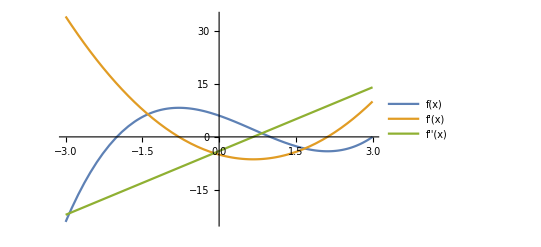

```mathematica
(* 对函数及其导数进行绘制图形 *)
Plot[{f[x],f'[x],f''[x]},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
(* 构建表格 *)
Table[{f[x],f'[x],f''[x]},{x,0,10}]
```

{{6,-5,-4},{0,-6,2},{-4,-1,8},{0,10,14},{18,27,20},{56,50,26},{120,79,32},{216,114,38},{350,155,44},{528,202,50},{756,255,56}}

```mathematica
TableForm[{{6,-5,-4},{0,-6,2},{-4,-1,8},{0,10,14},{18,27,20},{56,50,26},{120,79,32},{216,114,38},{350,155,44},{528,202,50},{756,255,56}}]
```

6 | -5 | -4
0 | -6 | 2
-4 | -1 | 8
0 | 10 | 14
18 | 27 | 20
56 | 50 | 26
120 | 79 | 32
216 | 114 | 38
350 | 155 | 44
528 | 202 | 50
756 | 255 | 56

```mathematica
Table[{f[x],f'[x],f''[x]},{x,0,10}] // TableForm (* 在二维表格的一位输出形式后面加上// TableForm表示输出为表格形式 *)
```

6 | -5 | -4
0 | -6 | 2
-4 | -1 | 8
0 | 10 | 14
18 | 27 | 20
56 | 50 | 26
120 | 79 | 32
216 | 114 | 38
350 | 155 | 44
528 | 202 | 50
756 | 255 | 56

```mathematica
(* 支持多个变量的微分计算 *)
D[x^2 Cos[x y]+y^2 Sin[x y],x]
```

2 x Cos[x y]+y^3 Cos[x y]-x^2 y Sin[x y]

```mathematica
D[%,y]
```

-x^3 y Cos[x y]+3 y^2 Cos[x y]-3 x^2 Sin[x y]-x y^3 Sin[x y]

```mathematica
D[x^2 Cos[x y]+y^2 Sin[x y],x,y] (* 表示先对x求导数在对y求导数 *)
```

-x^3 y Cos[x y]+3 y^2 Cos[x y]-3 x^2 Sin[x y]-x y^3 Sin[x y]

```mathematica
D[Sin[x]^10,{x,4}]
```

5040 Cos[x]^4 Sin[x]^6-4680 Cos[x]^2 Sin[x]^8+280 Sin[x]^10

```mathematica
Simplify[%]
```

10 (141+238 Cos[2 x]+125 Cos[4 x]) Sin[x]^6

```mathematica
D[x g[x],x]
```

g[x]+x g'[x]

```mathematica
D[x g[x],{x,2}]
```

2 g'[x]+x g''[x]

```mathematica
(* 规则替换 规则 /. 替换程式 *)
D[g[x^2]g''[x],x]/.g->Sin
```

-2 x Cos[x^2] Sin[x]-Cos[x] Sin[x^2]

```mathematica
(* 极限 *)
Limit[1/x,x->1]
```

1

```mathematica
Limit[√x,x->Infinity]
```

∞

```mathematica
Limit[√x,x->∞]
```

∞

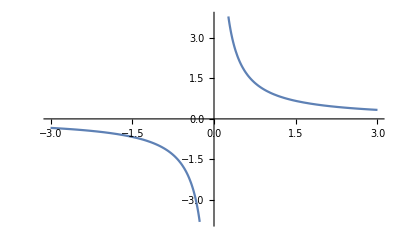

```mathematica
Plot[1/x,{x,-3,3}]
```

```mathematica
Limit[1/x,x->0,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->"FromAbove"]
```

∞

```mathematica
Limit[1/x,x->0]
```

Indeterminate

```mathematica
Information[Indeterminate]
```

```mathematica
f[x_]:=Piecewise[{{x, x<-1}, {x^2, x>=-1}}](*Ctrl+Enter加一行*)
```

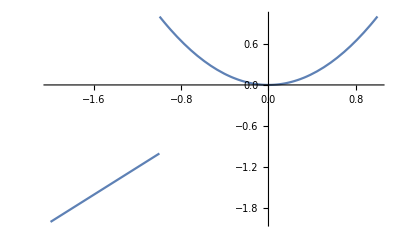

```mathematica
Plot[f[x],{x,-2,1}]
```

```mathematica
(* 为函数计算左极限与右极限 *)
Limit[f[x],x->1,Direction->"FromAbove"]
```

1

```mathematica
Limit[f[x],x->-1,Direction->"FromBelow"]
```

-1

```mathematica
Limit[x^a,a->∞]
```

ConditionalExpression[0, Log[x]<0]

```mathematica
(* Assumption条件指令加入限制条件 *)
Limit[x^a,a->∞,Assumptions->x>1]
```

∞

```mathematica
Limit[x^a,a->Ifinity,Assumptions->x==1]
```

1

```mathematica
Limit[x^a,a->Infinity,Assumptions->-1<x<0]
```

0

```mathematica
(* 积分 *)
Integrate[x^2+2x+1,x]
```

x+x^2+x^3/3

```mathematica
∫(x^2+2x+1)ⅆx (* 这一块必须加上括号 *)
```

x+x^2+x^3/3

```mathematica
∫(Sin[x])ⅆx
```

-Cos[x]

```mathematica
(* 失败的例子 *)
∫Sin[x]+Cos[x]ⅆx var
```

Integrate::nodiffd: ∫Sin[x] 无法解释. 可用格式 ∫fⅆx, ∫_a^b ，或者 ∫_(vars ∈ region)  输入积分，其中，可用 EscddEsc 输入 ⅆ.

-1/2 Cos[x]^2

```mathematica
(* 定积分 *)
Integrate[x^2,{x,0,2}]
```

8/3

```mathematica
Integrate[x^2 e^x,{x,0,1}]
```

(-2+2 e-2 e Log[e]+e Log[e]^2)/Log[e]^3

```mathematica
Integrate[x^2 ⅇ^2,{x,0,2}]
```

(8 ⅇ^2)/3

```mathematica
Integrate[x^2 ⅇ^x,{x,a,b}]
```

-((2+(-2+a) a) ⅇ^a)+(2+(-2+b) b) ⅇ^b

```mathematica
(* 边界包含函数值或者符号的情况 *)
Integrate[x^2 ⅇ^x,{x,0,a}]
```

-2+(2+(-2+a) a) ⅇ^a

```mathematica
Manipulate[
	Integrate[x^2 ⅇ^x,{x,0,a}],
{a,0,8}
]
```

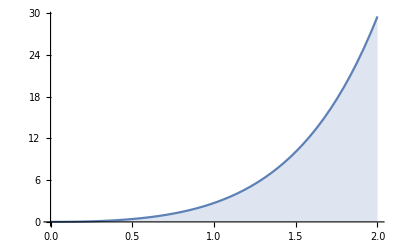

```mathematica
Plot[x^2 ⅇ^x,{x,0,2},Filling->Axis]
```

```mathematica
Manipulate[Plot[x^2 ⅇ^x,{x,0,t},Filling->Axis],{t,1,10}]
```

```mathematica
Manipulate[Plot[x^2 ⅇ^x,{x,0,t},Filling->Axis,PlotLabel->StringJoin["积分结果为:",ToString[Integrate[x^2 ⅇ^x,{x,0,t}]]]],{t,1,10}]
```

```mathematica
(* 使用数学助手面板进行输入 *)
∫_a^b Sin[x]ⅆx
```

Cos[a]-Cos[b]

```mathematica
(* Integrate返回精确结果 *)
Integrate[x^2 ⅇ^x,{x,0,1}]
```

-2+ⅇ

```mathematica
N[%]
```

0.718282

```mathematica
0.7182818284590451
```

0.718282

```mathematica
NIntegrate[x^2 ⅇ^x,{x,0,1}] (*近似的数值积分的结果*)
```

0.718282

```mathematica
(* 求解多重积分 积分变量的顺序是从外到内 *)
Integrate[x^2 Sin[y]+y^2 Cos[x],{x,-1,1},{y,-2,2}] (* 先对y后对x进行积分*)
```

(32 Sin[1])/3

```mathematica
(* 一般形式的二重积分 *)
∫_-1^1 ∫_-2^x (x^3 Sin[y]+y^2 Cos[x^2])ⅆyⅆx
```

8/3 √(2 π) FresnelC[√(2/π)]

```mathematica
(* 使用嵌套的一重积分用于二重积分 *)
Integrate[
	Integrate[
	x^3 Sin[y]+y^2 Cos[x],{y,-2,2}
],{x,-2,2}
]
```

(32 Sin[2])/3

```mathematica
Clear[f]
```